```mathematica
Clear[H,A,B,x1,x0,psi,out,Dmat,d1,d2,d3,d4,psi0,U,Re0,Re1,Im1,Im0]
Clear[sigX,sigZ,sigY,theta1,theta2,theta3,alpha]


A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];

sigX = PauliMatrix[1];t
sigY = PauliMatrix[2];
sigZ = PauliMatrix[3];

(*rz[theta_] = Exp[-I*theta*sigZ/2];*)
rz[theta_] = Cos[theta/2]*IdentityMatrix[2] - I*Sin[theta/2]*sigZ;
rx[theta_] =Cos[theta/2]*IdentityMatrix[2] - I*Sin[theta/2]*sigX;

Print["Rotation U:"]
buildU[alpha_,theta1_,theta2_,theta3_]:= Exp[I*alpha]*rz[theta1].rx[theta2].rz[theta3];
U = buildU[alpha,theta1,theta2,theta3];
Print[MatrixForm[U]]
(*A = IdentityMatrix[2];
B= IdentityMatrix[2];*)

(*U = {{u1,u2},{u3,u4}};*)

H = 1/(Sqrt[2])*{{1,1},{1,-1}};
Print["Eqs:"]
eqs = Thread[Flatten/@(U==H)]
Print["Sovling for rotation angles"]
sol = Solve[eqs,{alpha,theta1,theta2,theta3}];
Normal[sol] /.{C[1]->1,C[2]->1,C[3]->1,C[4]->1}
```

Rotation U:

(ⅇ^(ⅈ alpha) Cos[theta2/2] (Cos[theta1/2]-ⅈ Sin[theta1/2]) (Cos[theta3/2]-ⅈ Sin[theta3/2]) | -ⅈ ⅇ^(ⅈ alpha) (Cos[theta1/2]-ⅈ Sin[theta1/2]) Sin[theta2/2] (Cos[theta3/2]+ⅈ Sin[theta3/2])
-ⅈ ⅇ^(ⅈ alpha) (Cos[theta1/2]+ⅈ Sin[theta1/2]) Sin[theta2/2] (Cos[theta3/2]-ⅈ Sin[theta3/2]) | ⅇ^(ⅈ alpha) Cos[theta2/2] (Cos[theta1/2]+ⅈ Sin[theta1/2]) (Cos[theta3/2]+ⅈ Sin[theta3/2]))

Eqs:

{ⅇ^(ⅈ alpha) Cos[theta2/2] (Cos[theta1/2]-ⅈ Sin[theta1/2]) (Cos[theta3/2]-ⅈ Sin[theta3/2])==1/(√2),-ⅈ ⅇ^(ⅈ alpha) (Cos[theta1/2]-ⅈ Sin[theta1/2]) Sin[theta2/2] (Cos[theta3/2]+ⅈ Sin[theta3/2])==1/(√2),-ⅈ ⅇ^(ⅈ alpha) (Cos[theta1/2]+ⅈ Sin[theta1/2]) Sin[theta2/2] (Cos[theta3/2]-ⅈ Sin[theta3/2])==1/(√2),ⅇ^(ⅈ alpha) Cos[theta2/2] (Cos[theta1/2]+ⅈ Sin[theta1/2]) (Cos[theta3/2]+ⅈ Sin[theta3/2])==-1/(√2)}

Sovling for rotation angles

{{alpha→(3 π)/2,theta1→(5 π)/2,theta2→(5 π)/2,theta3→(5 π)/2},{alpha→(3 π)/2,theta1→(5 π)/2,theta2→(9 π)/2,theta3→(9 π)/2},{alpha→(3 π)/2,theta1→(7 π)/2,theta2→(7 π)/2,theta3→(7 π)/2},{alpha→(3 π)/2,theta1→(7 π)/2,theta2→(11 π)/2,theta3→(11 π)/2},{alpha→(3 π)/2,theta1→(9 π)/2,theta2→(5 π)/2,theta3→(9 π)/2},{alpha→(3 π)/2,theta1→(9 π)/2,theta2→(9 π)/2,theta3→(5 π)/2},{alpha→(3 π)/2,theta1→(11 π)/2,theta2→(7 π)/2,theta3→(11 π)/2},{alpha→(3 π)/2,theta1→(11 π)/2,theta2→(11 π)/2,theta3→(7 π)/2},{alpha→(5 π)/2,theta1→(5 π)/2,theta2→(5 π)/2,theta3→(9 π)/2},{alpha→(5 π)/2,theta1→(5 π)/2,theta2→(9 π)/2,theta3→(5 π)/2},{alpha→(5 π)/2,theta1→(7 π)/2,theta2→(7 π)/2,theta3→(11 π)/2},{alpha→(5 π)/2,theta1→(7 π)/2,theta2→(11 π)/2,theta3→(7 π)/2},{alpha→(5 π)/2,theta1→(9 π)/2,theta2→(5 π)/2,theta3→(5 π)/2},{alpha→(5 π)/2,theta1→(9 π)/2,theta2→(9 π)/2,theta3→(9 π)/2},{alpha→(5 π)/2,theta1→(11 π)/2,theta2→(7 π)/2,theta3→(7 π)/2},{alpha→(5 π)/2,theta1→(11 π)/2,theta2→(11 π)/2,theta3→(11 π)/2}}

```mathematica
U =H;
Dmat= DiagonalMatrix[{d1,d2,d3,d4}];

x0 = 1/Sqrt[2];
x1= -1/Sqrt[2];

psi0 ={x0,0,x1,0};

"A tensor H";
AtH= ArrayFlatten[TensorProduct[A,U]];
"H tensor B";
HtB = ArrayFlatten[TensorProduct[U,B]];

"HtB D AtH";
finalMat = Simplify[HtB.Dmat.AtH];

"Final Product";
phi =( finalMat.psi0)[[{1,2}]]//Normalize//Simplify;
"No Gadget:";
psi = B.H.A.{x0,x1};
```

```mathematica
Print["Minimizations"]
Re0 = Abs[Re[psi[[1]]] - Re[phi[[1]]]]^2;
Re1 = Abs[Re[psi[[2]]] - Re[phi[[2]]]]^2; 
Im0 = Abs[(Im[psi[[1]]] - Im[phi[[1]]])]^2; 
Im1 = Abs[(Im[psi[[2]]]-  Im[phi[[2]]])]^2;

t = {0,0,0,0};
For[i = 0,i < 100,i++,t = t + NArgMin[Re0 + Re1 + Im0 + Im1,{d1,d2,d3,d4}]]


t = t/Mean[Abs[t]];
Print["Value of t:" ]
Print[t]

Dmat2 = DiagonalMatrix[t];
newFinal =  Simplify[HtB.Dmat2.AtH];
phi2 = ( newFinal.psi0)[[{1,2}]]//Normalize//Simplify;

printer = Abs[{phi2[[1]],phi2[[2]],psi[[1]],psi[[2]]}]^2;

Print["phi 2:"]
Print[phi2]
Print["OG"]
Print[psi]
Print["overlap:"]
Print[prod[phi2,psi]]
Print[printer]
listEQ = {Re0,Re1,Im0,Im1};
```

Minimizations

Value of t:

{1.,1.,1.,-1.}

phi 2:

{-0.309606+0.241988 ⅈ,0.538686-0.745253 ⅈ}

OG

{-0.309606+0.241988 ⅈ,0.538686-0.745253 ⅈ}

overlap:

prod[{-0.309606+0.241988 ⅈ,0.538686-0.745253 ⅈ},{-0.309606+0.241988 ⅈ,0.538686-0.745253 ⅈ}]

{0.154414,0.845586,0.154414,0.845586}

```mathematica
getArgMins[psi_,phi_,params_]:= Module[{Re0,Re1,Im0,Im1},
Re0 = Abs[Re[psi[[1]]] - Re[phi[[1]]]]^2;
Re1 = Abs[Re[psi[[2]]] - Re[phi[[2]]]]^2; 
Im0 = Abs[(Im[psi[[1]]] - Im[phi[[1]]])]^2; 
Im1 = Abs[(Im[psi[[2]]]-  Im[phi[[2]]])]^2;
Return[NArgMin[Re0+Re1+Im0+Im1,params]]
]
```

```mathematica
getAverageOverlap[alpha_,theta1_,theta2_,theta3_]:= Module[{A,B,psi,psi0,t,AtU,UtB,Dmat,d1,d2 ,d3,d4,finalMat,phi,temp,tot,U,n},
n = 1000;
t = {0,0,0,0};
U = buildU[alpha,theta1,theta2,theta3];
For[i=0,i<n,i++,
(*Print[StringForm["First For Loop: ``" ,i]];*)
A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
psi0 = Normalize[RandomComplex[{-1-I,1+I},2]];
psi = B.H.A.psi0;
psi0 = {psi0[[1]],0,psi0[[2]],0};
AtU= ArrayFlatten[TensorProduct[A,U]];
UtB = ArrayFlatten[TensorProduct[U,B]];
Dmat = DiagonalMatrix[{d1,d2,d3,d4}];
finalMat = UtB.Dmat.AtU;

phi = finalMat.psi0;
phi = phi[[1;;2]]//Normalize//Simplify;
temp = getArgMins[psi,phi,{d1,d2,d3,d4}];
t = t +temp  ;
(*Print[StringForm["Output temp: ``",temp]];*)
];
(*Print[StringForm["Average t: ``",t/n]];*)
t = t/Mean[Abs[t]];
(*Print[StringForm["Final t: ``",t]];*)
Dmat = DiagonalMatrix[t];
tot = 0;

For[i=0,i<n,i++,
(*Print[StringForm["Second For Loop:``" ,i]];*)
A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
psi0 = Normalize[RandomComplex[{-1-I,1+I},2]];
psi = B.H.A.psi0;
psi0 = {psi0[[1]],0,psi0[[2]],0};
AtU= ArrayFlatten[TensorProduct[A,U]];
UtB = ArrayFlatten[TensorProduct[U,B]];
finalMat = UtB.Dmat.AtU;
phi = finalMat.psi0;
phi = phi[[1;;2]]//Normalize//Simplify;
tot =tot + prod[phi,psi];
];
(*Print[StringForm["Final Average Overlap: ``",tot/n]];*)
Return[Abs[tot/n]]
]

getAvgOverlapList[list_]:=getAverageOverlap[list[[1]],list[[2]],list[[3]],list[[4]]]
(*tab=Table[NMaximize[getAverageOverlap[a,i,j,b],{a,b}],{i,-Pi/2,Pi/2,0.1},{j,-Pi/2,Pi/2,0.1}]*)
```

```mathematica
373*50/60//N
```

310.833

NArgMin::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NArgMin::cvmit will be suppressed during this calculation.

NArgMin::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NArgMin::cvmit will be suppressed during this calculation.

Time Elapsed 1: 3717.4

Time Elapsed 2: 3751.97

./horizontalData.csv

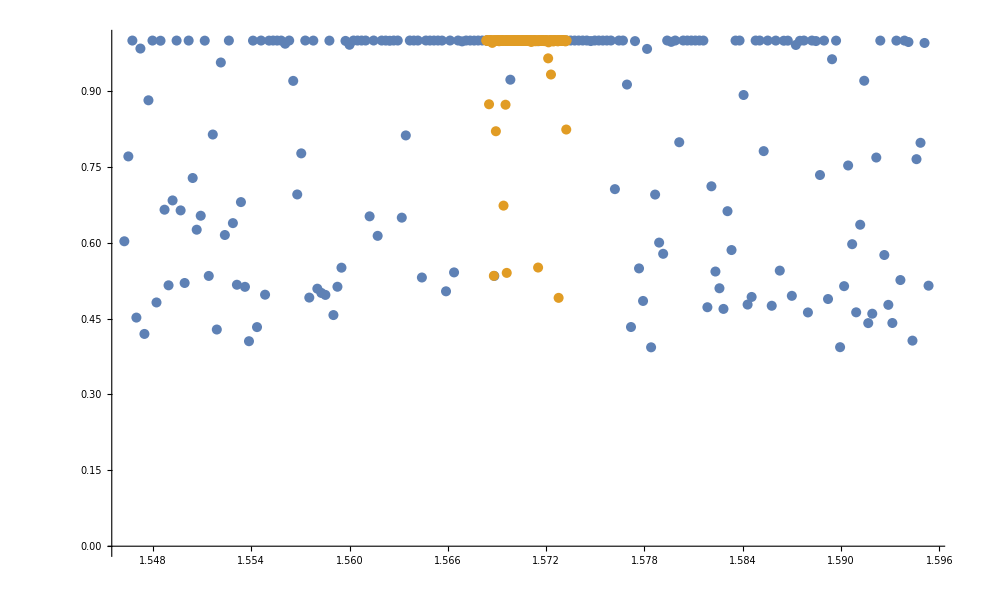

```mathematica
dx = Pi/(64*200);
dy = dx/10;
a = Pi/2 - 100*dx;
b = Pi/2 + 100*dx;
ay = Pi/2 - 100*dy;
by = Pi/2 + 100*dy;
xAxis = AbsoluteTiming[Table[{i,h[{i,Pi/2}]},{i,a,b,dx}]];
yAxis = AbsoluteTiming[Table[{i,h[{i,Pi/2}]},{i,ay,by,dy}]];
Print[StringForm["Time Elapsed 1: ``",xAxis[[1]]]]
Print[StringForm["Time Elapsed 2: ``",yAxis[[1]]]]
xAxis = xAxis[[2]];
yAxis = yAxis[[2]];
Export["./horizontalData.csv",xAxis]
ListPlot[{xAxis,yAxis}]
(*time = AbsoluteTiming[Map[h,xAxis]];
yAxis = time[[2]];
Print[StringForm["Time Elapsed: ``",time[[1]]]]
yAxis = Table[Append[xAxis[[i]],yAxis[[i]]],{i,1,Length[newTab]}]*)
```

~/Desktop/urop/qcomp-urop/horizontalDataLarge.csv

~/Desktop/urop/qcomp-urop/horizontalDataSmall.csv

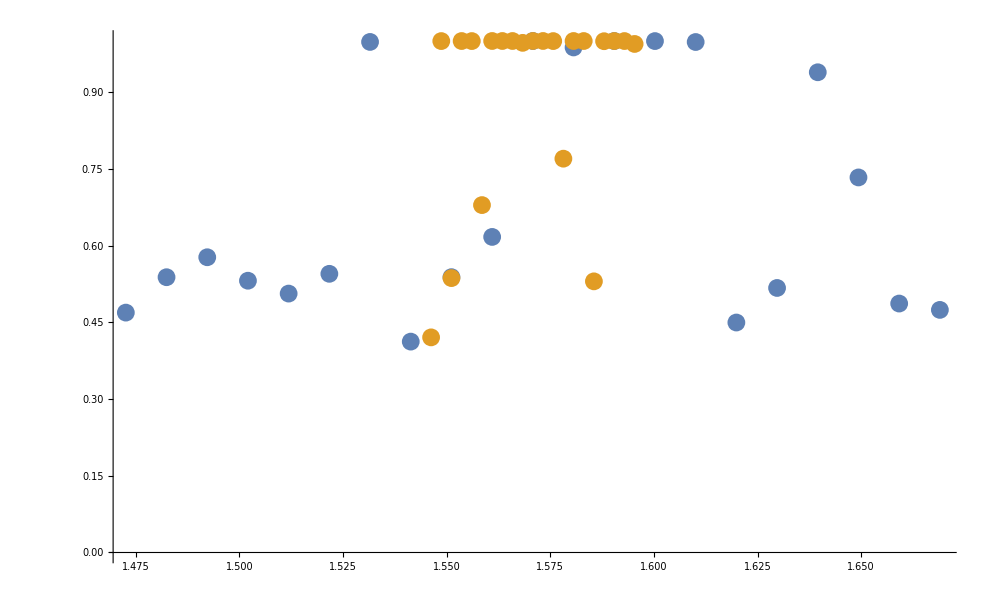

```mathematica
Export["~/Desktop/urop/qcomp-urop/horizontalDataLarge.csv",xAxis]
Export["~/Desktop/urop/qcomp-urop/horizontalDataSmall.csv",yAxis]
```

```mathematica
h[a_] := getAverageOverlap[Pi/2,a[[1]],a[[2]],Pi/2]
tab0 =  Table[{i,j},{i,7Pi/16,9Pi/16,Pi/(64)},{j,3Pi/8,5Pi/8,Pi/16}]
tab0 = Flatten[tab0,1]
time = AbsoluteTiming[Map[h,tab0]];
Print[StringForm["Total Time elapsed: ``",time[[1]]]]
newTab = time[[2]];
Export["data.csv",newTab]
plotter = Table[Append[tab0[[i]],newTab[[i]]],{i,1,Length[newTab]}]
Export["plotter.csv",plotter]
```

{{{(7 π)/16,(3 π)/8},{(7 π)/16,(7 π)/16},{(7 π)/16,π/2},{(7 π)/16,(9 π)/16},{(7 π)/16,(5 π)/8}},{{(29 π)/64,(3 π)/8},{(29 π)/64,(7 π)/16},{(29 π)/64,π/2},{(29 π)/64,(9 π)/16},{(29 π)/64,(5 π)/8}},{{(15 π)/32,(3 π)/8},{(15 π)/32,(7 π)/16},{(15 π)/32,π/2},{(15 π)/32,(9 π)/16},{(15 π)/32,(5 π)/8}},{{(31 π)/64,(3 π)/8},{(31 π)/64,(7 π)/16},{(31 π)/64,π/2},{(31 π)/64,(9 π)/16},{(31 π)/64,(5 π)/8}},{{π/2,(3 π)/8},{π/2,(7 π)/16},{π/2,π/2},{π/2,(9 π)/16},{π/2,(5 π)/8}},{{(33 π)/64,(3 π)/8},{(33 π)/64,(7 π)/16},{(33 π)/64,π/2},{(33 π)/64,(9 π)/16},{(33 π)/64,(5 π)/8}},{{(17 π)/32,(3 π)/8},{(17 π)/32,(7 π)/16},{(17 π)/32,π/2},{(17 π)/32,(9 π)/16},{(17 π)/32,(5 π)/8}},{{(35 π)/64,(3 π)/8},{(35 π)/64,(7 π)/16},{(35 π)/64,π/2},{(35 π)/64,(9 π)/16},{(35 π)/64,(5 π)/8}},{{(9 π)/16,(3 π)/8},{(9 π)/16,(7 π)/16},{(9 π)/16,π/2},{(9 π)/16,(9 π)/16},{(9 π)/16,(5 π)/8}}}

{{(7 π)/16,(3 π)/8},{(7 π)/16,(7 π)/16},{(7 π)/16,π/2},{(7 π)/16,(9 π)/16},{(7 π)/16,(5 π)/8},{(29 π)/64,(3 π)/8},{(29 π)/64,(7 π)/16},{(29 π)/64,π/2},{(29 π)/64,(9 π)/16},{(29 π)/64,(5 π)/8},{(15 π)/32,(3 π)/8},{(15 π)/32,(7 π)/16},{(15 π)/32,π/2},{(15 π)/32,(9 π)/16},{(15 π)/32,(5 π)/8},{(31 π)/64,(3 π)/8},{(31 π)/64,(7 π)/16},{(31 π)/64,π/2},{(31 π)/64,(9 π)/16},{(31 π)/64,(5 π)/8},{π/2,(3 π)/8},{π/2,(7 π)/16},{π/2,π/2},{π/2,(9 π)/16},{π/2,(5 π)/8},{(33 π)/64,(3 π)/8},{(33 π)/64,(7 π)/16},{(33 π)/64,π/2},{(33 π)/64,(9 π)/16},{(33 π)/64,(5 π)/8},{(17 π)/32,(3 π)/8},{(17 π)/32,(7 π)/16},{(17 π)/32,π/2},{(17 π)/32,(9 π)/16},{(17 π)/32,(5 π)/8},{(35 π)/64,(3 π)/8},{(35 π)/64,(7 π)/16},{(35 π)/64,π/2},{(35 π)/64,(9 π)/16},{(35 π)/64,(5 π)/8},{(9 π)/16,(3 π)/8},{(9 π)/16,(7 π)/16},{(9 π)/16,π/2},{(9 π)/16,(9 π)/16},{(9 π)/16,(5 π)/8}}

Total Time elapsed: 110.453

data.csv

{{(7 π)/16,(3 π)/8,0.994176},{(7 π)/16,(7 π)/16,0.581815},{(7 π)/16,π/2,0.455733},{(7 π)/16,(9 π)/16,0.343565},{(7 π)/16,(5 π)/8,0.468524},{(29 π)/64,(3 π)/8,0.378788},{(29 π)/64,(7 π)/16,0.989089},{(29 π)/64,π/2,0.528739},{(29 π)/64,(9 π)/16,0.665596},{(29 π)/64,(5 π)/8,0.436808},{(15 π)/32,(3 π)/8,0.991289},{(15 π)/32,(7 π)/16,0.481484},{(15 π)/32,π/2,0.521128},{(15 π)/32,(9 π)/16,0.9967},{(15 π)/32,(5 π)/8,0.535146},{(31 π)/64,(3 π)/8,0.635796},{(31 π)/64,(7 π)/16,0.994971},{(31 π)/64,π/2,0.498956},{(31 π)/64,(9 π)/16,0.436945},{(31 π)/64,(5 π)/8,0.99957},{π/2,(3 π)/8,1.},{π/2,(7 π)/16,1.},{π/2,π/2,1.},{π/2,(9 π)/16,1.},{π/2,(5 π)/8,1.},{(33 π)/64,(3 π)/8,0.998907},{(33 π)/64,(7 π)/16,0.528187},{(33 π)/64,π/2,0.584051},{(33 π)/64,(9 π)/16,0.998453},{(33 π)/64,(5 π)/8,0.983858},{(17 π)/32,(3 π)/8,0.997085},{(17 π)/32,(7 π)/16,0.328812},{(17 π)/32,π/2,0.669747},{(17 π)/32,(9 π)/16,0.991953},{(17 π)/32,(5 π)/8,0.990326},{(35 π)/64,(3 π)/8,0.996652},{(35 π)/64,(7 π)/16,0.991177},{(35 π)/64,π/2,0.996011},{(35 π)/64,(9 π)/16,0.56667},{(35 π)/64,(5 π)/8,0.418337},{(9 π)/16,(3 π)/8,0.412932},{(9 π)/16,(7 π)/16,0.983173},{(9 π)/16,π/2,0.979299},{(9 π)/16,(9 π)/16,0.571411},{(9 π)/16,(5 π)/8,0.547783}}

plotter.csv

7.85398

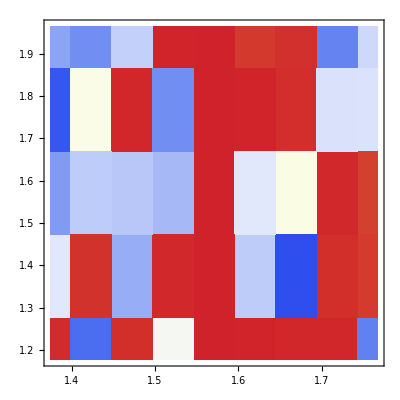

-Graphics3D-

```mathematica
newTab;
5Pi/2 //N
plotter = Table[Append[tab0[[i]],newTab[[i]]],{i,1,Length[newTab]}];
ListDensityPlot[plotter,InterpolationOrder->0,ColorFunction->"TemperatureMap"]
ListPlot3D[plotter]
```

```mathematica
constructPhi[alpha_,beta_,Unitary_,D_]:= Module[{psi,A,B,AtU,UtB,finalMat,phi},
psi  = {alpha,0,beta,0}//Normalize;
A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
AtU = ArrayFlatten[TensorProduct[A,Unitary]];
UtB = ArrayFlatten[TensorProduct[Unitary,B]];
finalMat =  Simplify[UtB.D.AtU];
phi = ( finalMat.psi0)[[{1,2}]]//Normalize//Simplify;
Return[phi];
]
```

```mathematica
Clear[t,m1,m2,m3,m4]
prod[psi_,phi_]:=( psi.Conjugate[phi])*(phi.Conjugate[psi])
f[AtU_,UtB_,d1_,d2_,d3_,d4_]:= Module[{Dmat,phi,Re0,Re1,Im0,Im1},
Dmat = DiagonalMatrix[{d1,d2,d3,d4}];
phi = (UtB.Dmat.AtU.psi0);
phi = phi[[1;;2]]//Normalize//Simplify;
Re0 = (Re[psi[[1]]] - Re[phi[[1]]])^2;
Re1 = (Re[psi[[2]]] - Re[phi[[2]]])^2;

Im0 = (Im[psi[[1]]] - Im[phi[[1]]])^2;
Im1 = (Im[psi[[2]]] - Im[phi[[2]]])^2;
Sum[i,{i,{Re0,Re1,Im0,Im1}}]
]

g[d1_,d2_,d3_,d4_]:=f[AtH,HtB,d1,d2,d3,d4]
"testing g"
Minimize[f[AtH,HtB,m1,m2,m3,m4],{m1,m2,m3,m4}]
```

testing g

{1.01473×10^-16,{m1→0.418778,m2→0.418778,m3→0.418778,m4→-0.418778}}

```mathematica
{{1,0},{0,-1}}.{{0,1},{1,0}}
```

{{0,1},{-1,0}}